# Time Dilation

## Vector Addition

In every day life, velocities of objects add like vectors. This means that the velocity of an object that you observe depends not only on the objects motion, but on your own motion as well.

V_AC=V_AB+V_BC

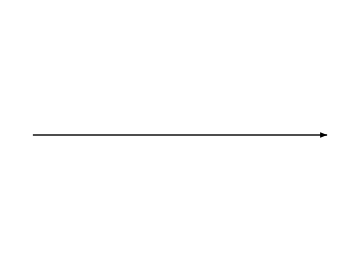

+

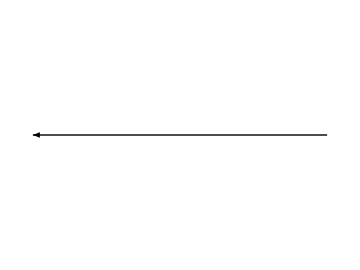

=

-Graphics-

```mathematica
Graphics[Arrow[{{0,0},{2,0}},{0,1}]]
Style["+",40,Bold]
Graphics[Arrow[{{2,0},{0,0}},{0,1}]]
Style["=",40,Bold]
Graphics[Arrow[{{2,0},{6,0}}]]
```

If you are sitting in a moving car and then throw a football straight upwards, you will see it as traveling this path :

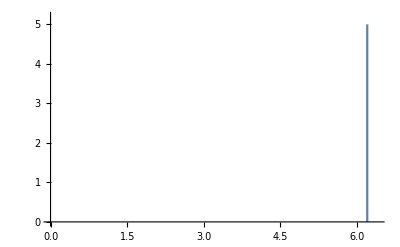

```mathematica
ListLinePlot[Table[{6.2,n},{n,0,5}],PlotRange->{{0,6.4},{0,5.2}}]
```

But a person standing on the sidewalk will see the ball travel a path like :

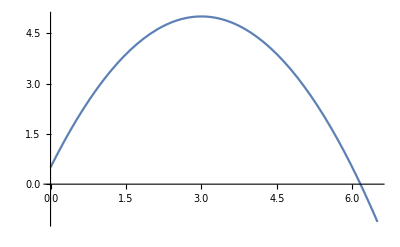

```mathematica
Plot[-1/2(x-3)^2+5,{x,0,6.5}]
```

The ball gets a velocity added in the horizontal direction for the sidewalk observer, making overall velocity of the ball greater.

## The Speed of Light

Velocities of objects may add, but this is NOT the case with light. Light has the same velocity (about 300000000 meters/sec) no matter the motion of observers or source.It will always travel at velocity "c".

```mathematica
ListLinePlot[Table[{6.2,n},{n,0,5}],PlotRange->{{0,6.4},{0,5.2}}]
```

-Graphics-

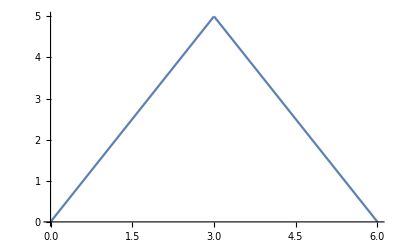

```mathematica
Plot[Piecewise[{{(5/3)x,x<3},{10-(5/3)x,x>3}}],{x,0,6}]
```

## Light Clock in a Car

Even if our light beam is in a car, it will have the same velocity, but we see that now the sidewalk observer sees it travelling a greater distance.

Since Distance = (Rate) * (Time), and rate is the same always, then for a larger distance, time must be larger as well. This is time dilataion.

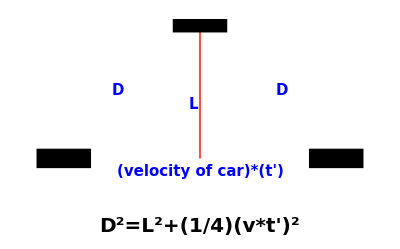

```mathematica
Graphics[
{EdgeForm[Thick],White,Triangle[{{0,0},{1,1},{2,0}}],
Style[Line[{{1,0},{1,1}}],Thick,Red],
Style[Line[{{-.2,0},{.2,0}}],Thickness[.035],Black],
Style[Line[{{.8,1},{1.2,1}}],Thickness[.035],Black],
Style[Line[{{1.8,0},{2.2,0}}],Thickness[.035],Black],
Rotate[Text[Style["L",15,Bold, Blue],{.95,.4}],90 Degree],
Rotate[Text[Style["D",15,Bold, Blue],{.4,.5}],48Degree],
Rotate[Text[Style["D",15,Bold, Blue],{1.6,.5}],-48Degree], 
Text[Style["(velocity of car)*(t')",15, Bold, Blue],{1,-.1}],
Text[Style["D^2=L^2+(1/4)(v*t')^2",20, Bold, Black],{1,-.5}]}]
```

In one bounce up and down, observer in the car sees light traveling a path 2*L, but an observer on the sidewalk sees it traveling a path 2*D

```mathematica
Style["1. 2(L)=(c)*(t)",Bold,20]
Style["2. 2(D)=(c)*(t')",Bold,20]
Style["3. D=√(L^2+1/4 v^2 (t')^2)",Bold,20]
Style["4. Plug in and solve:",Bold, 20]
Style["t'=(√(1/(1 - FractionBox[SuperscriptBox[v, 2], SuperscriptBox[c, 2]])))t , → γ=√(1/(1 - FractionBox[SuperscriptBox[v, 2], SuperscriptBox[c, 2]])) ",Bold, 20]
```

1. 2(L)=(c)*(t)

2. 2(D)=(c)*(t')

3. D=√(L^2+1/4 v^2 (t')^2)

4. Plug in and solve:

t'=(√(1/(1 - FractionBox[SuperscriptBox[v, 2], SuperscriptBox[c, 2]])))t , → γ=√(1/(1 - FractionBox[SuperscriptBox[v, 2], SuperscriptBox[c, 2]]))

What happens when v = 0? What happens when v -> c?

```mathematica
Manipulate[
GraphicsGrid[{{Graphics[
{ Disk[{V T, 1 -  FractionalPart[ver[V] T]},0.025],Disk[{V T, FractionalPart[ver[V] T]},0.025],(* moving light pulse *)
 Blue, Rectangle[{-1/8 + V T, -0.5/8}, {1/8 + V T, 0}], Rectangle[{-1 /8+ V T, 0.5}, {1/8 +V T, 4.5/8}], (*moving mirrors*)
Black,Disk[{0,FractionalPart[T]},0.025],Disk[{24/8,  FractionalPart[T]}, 0.025],(*upward component of light pulses in rest frame*)Disk[{0, 1-  FractionalPart[T]}, 0.025],Disk[{24/8, 1 -  FractionalPart[T]}, 0.025],(*downward component of light pulses in rest frame*)
 Rectangle[{-1.25/8, -0.5/8}, {1.25/8, 0}], Rectangle[{22.75/8, -0.5/8}, {25.25/8, 0}],Rectangle[{-1.25/8, 0.5}, {1.25/8, 4.5/8}],Rectangle[{22.75/8, 0.5}, {25.25/8, 4.5/8}], (*mirrors in rest frame*)
Dashed, Red, Line[{{period[V], 0}, {period[V]+ V/(2 ver[V]), 0}, {period[V]+ V/(2 ver[V]), 0.5}, {period[V], 0}}](*triangle depicting horizontal and vertical components of motion*)},
PlotRange -> {{-4/8, 28/8}, {-0.4/8, 4.4/8}},ImageSize ->{550,160}]},

{GraphicsRow[{Column[{Text[Style["stationary clock",18,Red,Bold]],Style[StringForm[If[IntegerPart[T]==1,"has recorded `` tick","has recorded `` ticks"],IntegerPart[T]],18,Red,Bold],,,Text[Style["moving clock",18,Red,Bold]],Style[StringForm[If[IntegerPart[If[V≠0,T V/period[V],T]]==1,"has recorded `` tick","has recorded `` ticks"],IntegerPart[If[V≠0,T V/period[V],T]]],18,Red,Bold]},Alignment->Center],GraphicsColumn[{
Text[Style[Row[{v," ≈ ",NumberForm[V,{3,2}]," ",c}],18,Red,Bold]],Text[Style[Row[{"γ ≈ ",NumberForm[(1-(V^2))^(-0.5),{3,2}]}],18,Red,Bold]]},ImageSize->{200,200},Alignment->{Left,Center}],Graphics[{Dashed, Red, Line[{{0, 0}, { V/(2 ver[V]), 0}, { V/(2 ver[V]), 0.5}, {0, 0}}],  Text[Style[L,18,Bold],{0.5/8+ V/(2 ver[V]), 0.25}], RGBColor[1,0,0,If[V≥0.25,1,V/0.25]],Text[Style[γ L,18,Bold], { V/(6 ver[V]), 0.25}],Text[Style[v γ L / c,18,Bold], {4.5 V/(16 ver[V]), 0.5/8}]}]}]}
},AspectRatio->Automatic,ImageSize->{600,360},ImageSize->{600,500}],

 {{T, 0,"time"},0,10,0.0001,DefaultDuration ->If[V≥0.1,60/V,15],AnimationRate->0.5,AppearanceElements->All},
{{V,0,"velocity"},0,0.9,AppearanceElements->All},
TrackedSymbols:>{T,V},
Initialization:>(
ver[m_]:=(1-m^2)^0.5;(*vertical component of motion of moving light pulse*)
period[k_]:=k(1-(k^2))^(-0.5);(*horizontal distance covered by moving light pulse between each tick*)
)]
```

We see how the blue one traces out a longer path but is traveling with the same speed, so it should take the light in the blue one longer to bounce up and down once. One “tick” is larger in that frame.